```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY197/sec_int_data/610nm.dat"]
```

{{1.50189,0.270027},{1.45414,0.276646},{1.33983,0.293192},{1.30748,0.29684},{1.27821,0.300179},{1.24682,0.286907},{1.22351,0.248967},{1.20659,0.21793},{1.18213,0.166531},{1.16419,0.132694},{1.15263,0.112078},{1.13304,0.08158},{1.09662,0.29788},{1.09807,0.278767},{1.10207,0.281186},{1.10747,0.280506},{1.11401,0.282469},{1.12685,0.295501},{1.13867,0.301733},{1.15401,0.300327},{1.16573,0.295055},{1.20258,0.293714},{1.26466,0.295129},{1.30748,0.288182},{1.33983,0.272695},{1.37936,0.275432}}

0.120784+0.112677 x

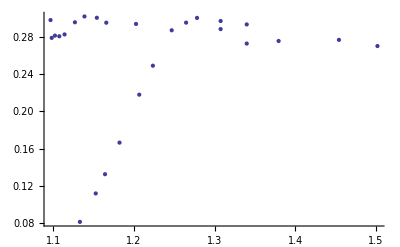

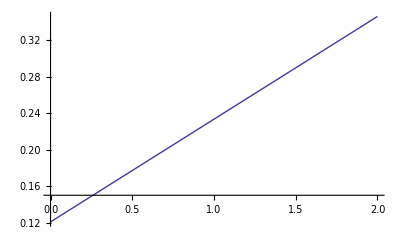

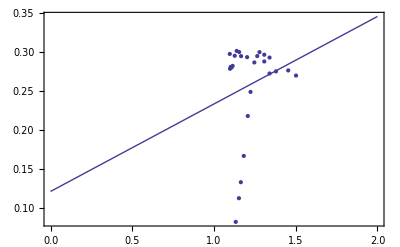

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```